```mathematica
f[x_]:=Piecewise[{{x^2 Sin[1/x], x<0}, {x, x≥0}}]
```

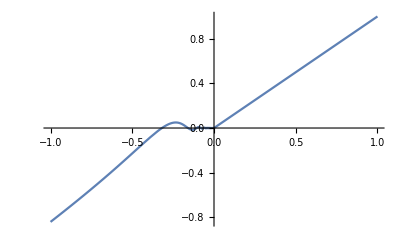

```mathematica
Plot[f[x],{x,-1,1}]
```

Piecewise[{{-Cos[1/x]+2 x Sin[1/x], x<0}, {1, x>0}, {Indeterminate, True}}]

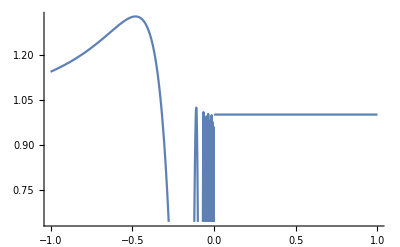

```mathematica
f'[x]
Plot[f'[x],{x,-1,1}]
```

```mathematica
W[0][x_]:=Min[x,0]
dW[0][x_]:=W[0]'[x]
dW[1][x_]:=Piecewise[{{1, x≤-1}, {(1-x)/2, -1<x<1}, {0, True}}]
dW[2][x_]:=Piecewise[{{1, x≤-2}, {1/8 (4-x^2), x==0}, {1/8 (4-4 x-x^2), -2<x<0}, {1/8 (4-4 x+x^2), 0<x<2}, {0, True}}]
dW[3][x_]:=Piecewise[{{1, x≤-3}, {1/48 (21-27 x-9 x^2-x^3), -3<x<-1}, {1/48 (45-3 x-9 x^2-x^3), x==-1}, {1/48 (27-27 x+9 x^2-x^3), 1<x<3}, {1/24 (12-9 x+x^3), -1<x<1}, {1/48 (7+3 x-3 x^2+x^3), x==1}, {0, True}}]
dW[n_][x_]:=Integrate[dW[n-1][x-2u+1],{u,0,1}]
```

Piecewise[{{0, x<-1}, {-1/2, -1<x<1}, {0, x>1}, {Indeterminate, True}}]

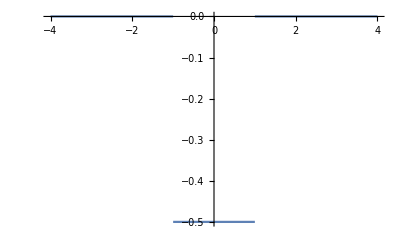

```mathematica
dW[1]'[x]
Plot[dW[1]'[x],{x,-4,4},PlotPoints->1000]
```